# Lower bounds

```mathematica
Quit
```

Define the problem and functions for computing associated properties:

```mathematica
getW[L_]:=Evaluate@{D[L[x,y],x],-D[L[x,y],y]};
F[x_,y_]:=a*x*y+b/2*x^2-b/2*y^2;
W[x_,y_]:=Evaluate@getW[F]
star={0,0};
weakMVIcondition[x_,y_]:=(W[x,y]).({x,y}-star)/Norm[W[x,y]]^2;
J[x_,y_]:=Evaluate@(D[W[x,y],{{x,y}}]);
LocalLips[x_,y_]:=SingularValueList[J[x,y],1][[1]];
```

Compute L and ρ  and the EG+ update:

```mathematica
Clear[a,b,c,α];
$Assumptions=a∈PositiveReals&&b∈NegativeReals&&x∈Reals&&y∈Reals&&α∈PositiveReals&&α<1&&c∈PositiveReals;
ρ=weakMVIcondition[x,y]//Simplify
L=LocalLips[x,y]//Simplify
γ=1/L;
EG[x_,y_]:=Module[{},
zbar={x,y}-γ*W[x,y];
{x,y}-α*γ*W[zbar[[1]],zbar[[2]]]];
update=EG[x,y]//Simplify;
T={{D[update,x][[1]],D[update,y][[1]]},
{D[update,x][[2]],D[update,y][[2]]}};
T//MatrixForm
```

b/(a^2+b^2)

√(a^2+b^2)

((a^2 (1-α)+b (b+b α-√(a^2+b^2) α))/(a^2+b^2) | -(a (-2 b+√(a^2+b^2)) α)/(a^2+b^2)
(a (-2 b+√(a^2+b^2)) α)/(a^2+b^2) | (a^2 (1-α)+b (b+b α-√(a^2+b^2) α))/(a^2+b^2))

Compute the spectral radius and solve given the constraint on ρ:

```mathematica
spectralrad=Max[Abs[Eigenvalues[T]]]//FullSimplify
Reduce[ρ==-c/L&&spectralrad<1,{c,a,b}]//FullSimplify
```

√((b^2-2 b (-b+√(a^2+b^2)) α (1+α)+a^2 (1+2 (-1+α) α))/(a^2+b^2))

b+(a c)/(√(1-c^2))==0&&2 c+α<1

Simplify further to plot:

```mathematica
Reduce[2 c+α<1,c]
```

α∈ℝ&&c<(1-α)/2

## Plotting

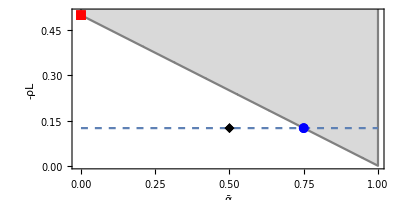

```mathematica
Show[RegionPlot[c>=(1-α)/2,{α,0,1},{c,0,1},
PlotStyle->{LightGray},
BoundaryStyle->{Gray},
PlotRange->{{-1/100,1},{0,1/2+1/100}},
FrameLabel->{"ᾱ","-ρL"},
AspectRatio->{1/2},
Frame->True],
Plot[1/8,{α,0,1},PlotStyle->Dashed],
ListPlot[{{{3/4,1/8}},{{0,1/2}},{{1/2,1/8}}},PlotMarkers->{Automatic,10},PlotStyle->{Blue,Red,Black}]]
```